# EQLab package quick guide.

## Useful Info

1) Some definitions:

1.1) USER         →    one of us, someone who runs this package.

1.2) predictor → an expert, a person whose behaviour/belief we try to model

1.3) question  →  a  basic  ‘unit’ in an experiment, indexed by ‘i’.  Asking a question (fixed i) is  a step that involves producing:
	a) forecasts  p_ij for each predictor ( for all values of   j )
	b) a measurement m_i (like tossing a die)
	c) resolutions v_ij for each predictor  ( for all values of   j ) 
	d) outcome q_i ( this reflects the resolution of the majority of predictors  )
	e) surprisals s_ij for each predictor  ( for all values of   j ) 
	f)  rewards r_ij  for each predictor  ( for all values of   j )  
	A question is stored in EQLab as a List :  question_i={p_i,m_i,v_i,q,s_i,r_i};  Where bold letters are each a List
	
1.4) Experiment → a set of questions asked in sequence (stored as a List of questions)

2)Some variable definitions:

2.1) npredictors →  number of  predictors  (cannot be modified after loading EQLab )
         nquestions →  number of  questions for each experiment (can be modified in between experiments)

2.2) npredictorsUSER →   number of  predictors, to be defined by user before  loading EQLab. (have no effect after loading)

## Steps to prepare simulations

Set user parameter values

```mathematica
npredictorsUSER=4;
```

Load package

```mathematica
$Path=Join[$Path,{NotebookDirectory[]}];
<<EQLab`
```

Define functions needed for experiment. Needs the follow the prototypes below:

UserPredict[exp_ , newquestion_]       →  Function should return a List of numbers (forecasts) of size ‘npredictors’ ;    ‘exp’  and ‘newquestion’  are  as defined in EQLab  it is useful if predictors update their forecast based on previous questions and/or current measurement .

```mathematica
(*set initial forecast*)
setforecastinit[]:=(forecastinit=Table[Random[],{i,1,npredictors}];);
forecastinit={9/10,5/10,1/10,1/10}//N;
(*random numbers M to model how each predictor 'reacts' for previous measurements*)
(*smaller M means more reactive*)
setreactioninit[]:=(reactivity=Table[RandomInteger[{1,20}],{i,1,npredictors}];)
reactivity={1,100,1,100};
UserPredict[exp_,newquestion_]:=Module[
{REACTIVITY=reactivity,M,ipredictor,n=(exp//Length),ρnew,ρ,m,RHOnew={}},


For[ipredictor=1,ipredictor≤npredictors,ipredictor++,
If[n==0,
ρnew=forecastinit[[ipredictor]],
ρ=exp[[n,1,ipredictor]];
m=exp[[n,2]];
M=REACTIVITY[[ipredictor]];
ρnew=1/(2 (M+n))+m/(2 (M+n))+((-1+M+n) ρ)/(M+n);
];
AppendTo[RHOnew,ρnew];];
RHOnew]
```

UserMeasure[] 	      →    Function should return either    +1 or -1.  (yes or no, like the toss of a die.)

```mathematica
prob=7/10;
UserMeasure[]:=(Random[]//Which[#<prob,1,True,-1]&);
```

UserResolve[exp_ , newquestion_]  	      →    Function should use the List  ‘newquestion[[1]]’ ( forecasts), and  return a List of numbers (resolutions) of the same size.  Arguments are   an experiment  and a question  as defined in EQLab. The variable ‘exp’ is useful only when modeling predictors that use knowledge from previous  questions in the experiment. Even If ‘exp’ is not used, the function must adhere to the  prototype.

```mathematica
UserResolve[experiment_,question_]:=UserResolve[question];
UserResolve[question_]:=Table[Random[]//Which[#<0.5,-question[[2]],True,question[[2]]]&,{i,1,question[[1]]//Length}]
```

## Perform Experiments

#### Results of experiments are stored in the List called ‘EXPERIMENT’

```mathematica
EXPERIMENT
```

{}

#### By default, EQLab loads some predefined functions, So you can run an experiment.

```mathematica
RunExperiment[]
```

#### Now EXPERIMENT has one element (one experiment)

```mathematica
EXPERIMENT//Length
```

1

#### One can run another experiment, and check the size of EXPERIMENT again

```mathematica
RunExperiment[]
EXPERIMENT//Length
```

2

#### See contents of experiment 1

```mathematica
EXPERIMENT[[1]]//MatrixForm
```

({0.199596,0.39117,0.232276,0.914471} | 1 | {1,1,1,1} | 1 | {1.61146,0.938613,1.45983,0.0894096} | {0.0689326,0.531162,0.1731,1.11454}
{0.199596,0.39117,0.232276,0.914471} | 1 | {1,1,1,1} | 1 | {1.61146,0.938613,1.45983,0.0894096} | {0.0689326,0.531162,0.1731,1.11454}
{0.199596,0.39117,0.232276,0.914471} | 1 | {1,1,1,1} | 1 | {1.61146,0.938613,1.45983,0.0894096} | {0.0689326,0.531162,0.1731,1.11454}
{0.199596,0.39117,0.232276,0.914471} | 1 | {1,1,-1,1} | 1 | {1.61146,0.938613,1.45983,0.0894096} | {0.0344663,0.265581,0.0865501,0.557272}
{0.199596,0.39117,0.232276,0.914471} | 1 | {-1,1,1,1} | 1 | {1.61146,0.938613,1.45983,0.0894096} | {0.0344663,0.265581,0.0865501,0.557272}
{0.199596,0.39117,0.232276,0.914471} | 1 | {1,1,1,1} | 1 | {1.61146,0.938613,1.45983,0.0894096} | {0.0689326,0.531162,0.1731,1.11454}
{0.199596,0.39117,0.232276,0.914471} | -1 | {-1,-1,-1,-1} | -1 | {0.222639,0.496216,0.264325,2.4589} | {1.834,1.54062,1.78929,-0.564081}
{0.199596,0.39117,0.232276,0.914471} | -1 | {-1,-1,-1,-1} | -1 | {0.222639,0.496216,0.264325,2.4589} | {1.834,1.54062,1.78929,-0.564081}
{0.199596,0.39117,0.232276,0.914471} | -1 | {-1,-1,-1,-1} | -1 | {0.222639,0.496216,0.264325,2.4589} | {1.834,1.54062,1.78929,-0.564081}
{0.199596,0.39117,0.232276,0.914471} | -1 | {-1,-1,-1,-1} | -1 | {0.222639,0.496216,0.264325,2.4589} | {1.834,1.54062,1.78929,-0.564081}
{0.199596,0.39117,0.232276,0.914471} | -1 | {-1,-1,-1,-1} | -1 | {0.222639,0.496216,0.264325,2.4589} | {1.834,1.54062,1.78929,-0.564081}
{0.199596,0.39117,0.232276,0.914471} | -1 | {-1,-1,-1,1} | -1 | {0.222639,0.496216,0.264325,2.4589} | {0.916998,0.770311,0.894647,-0.282041}
{0.199596,0.39117,0.232276,0.914471} | 1 | {1,1,1,1} | 1 | {1.61146,0.938613,1.45983,0.0894096} | {0.0689326,0.531162,0.1731,1.11454}
{0.199596,0.39117,0.232276,0.914471} | 1 | {1,1,1,1} | 1 | {1.61146,0.938613,1.45983,0.0894096} | {0.0689326,0.531162,0.1731,1.11454}
{0.199596,0.39117,0.232276,0.914471} | 1 | {1,1,1,1} | 1 | {1.61146,0.938613,1.45983,0.0894096} | {0.0689326,0.531162,0.1731,1.11454}
{0.199596,0.39117,0.232276,0.914471} | -1 | {-1,-1,-1,-1} | -1 | {0.222639,0.496216,0.264325,2.4589} | {1.834,1.54062,1.78929,-0.564081}
{0.199596,0.39117,0.232276,0.914471} | 1 | {1,1,1,-1} | 1 | {1.61146,0.938613,1.45983,0.0894096} | {0.0344663,0.265581,0.0865501,0.557272}
{0.199596,0.39117,0.232276,0.914471} | -1 | {1,-1,-1,-1} | -1 | {0.222639,0.496216,0.264325,2.4589} | {0.916998,0.770311,0.894647,-0.282041}
{0.199596,0.39117,0.232276,0.914471} | -1 | {-1,-1,-1,-1} | -1 | {0.222639,0.496216,0.264325,2.4589} | {1.834,1.54062,1.78929,-0.564081}
{0.199596,0.39117,0.232276,0.914471} | -1 | {-1,-1,-1,-1} | -1 | {0.222639,0.496216,0.264325,2.4589} | {1.834,1.54062,1.78929,-0.564081})

#### Use ShowPlots[] to see results for the lastest experiment (plots are stored in the ‘SUPERARRAY‘ called ‘PLOTS’. )

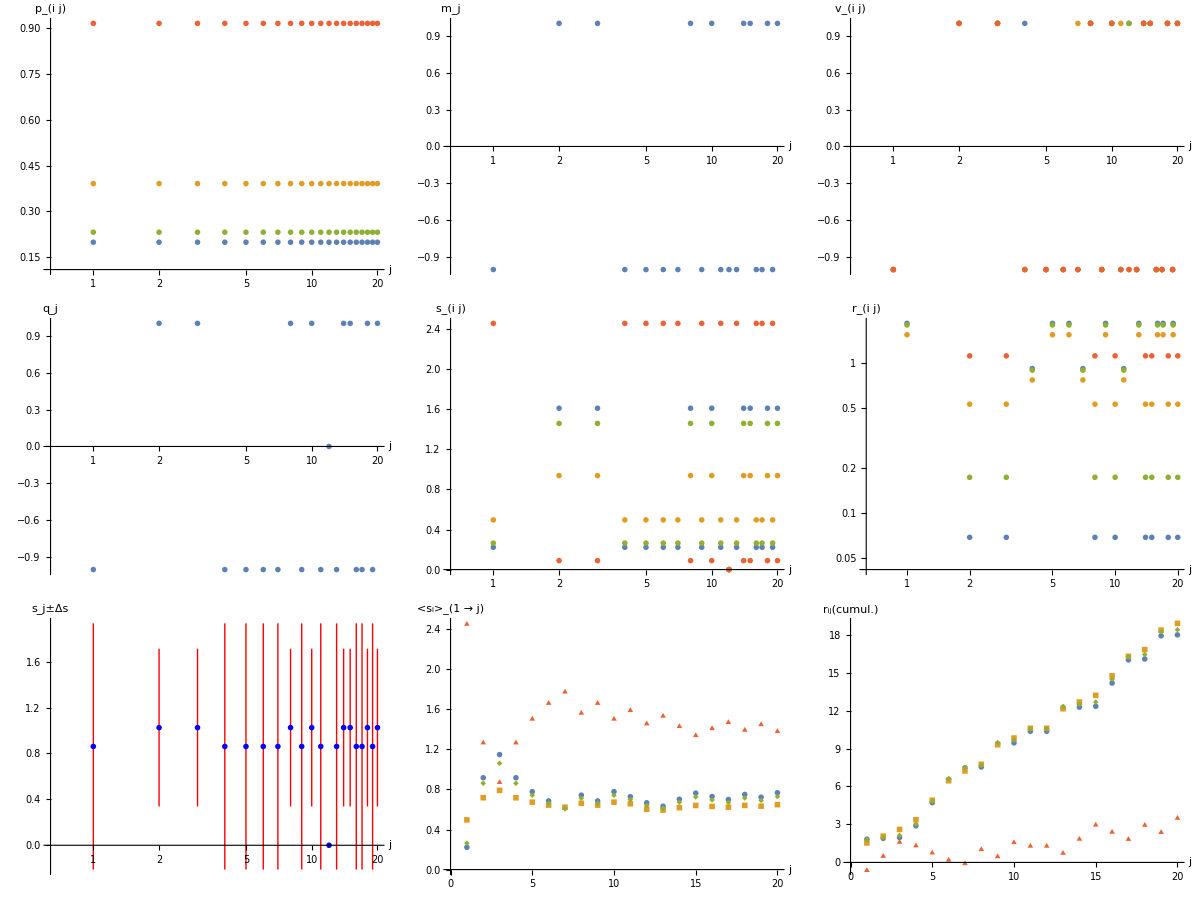

```mathematica
ShowPlots[]
```

#### Use ShowPlots[i] to see results for the ith experiment (plots are stored in the ‘SUPERARRAY‘ called ‘PLOTS’. )

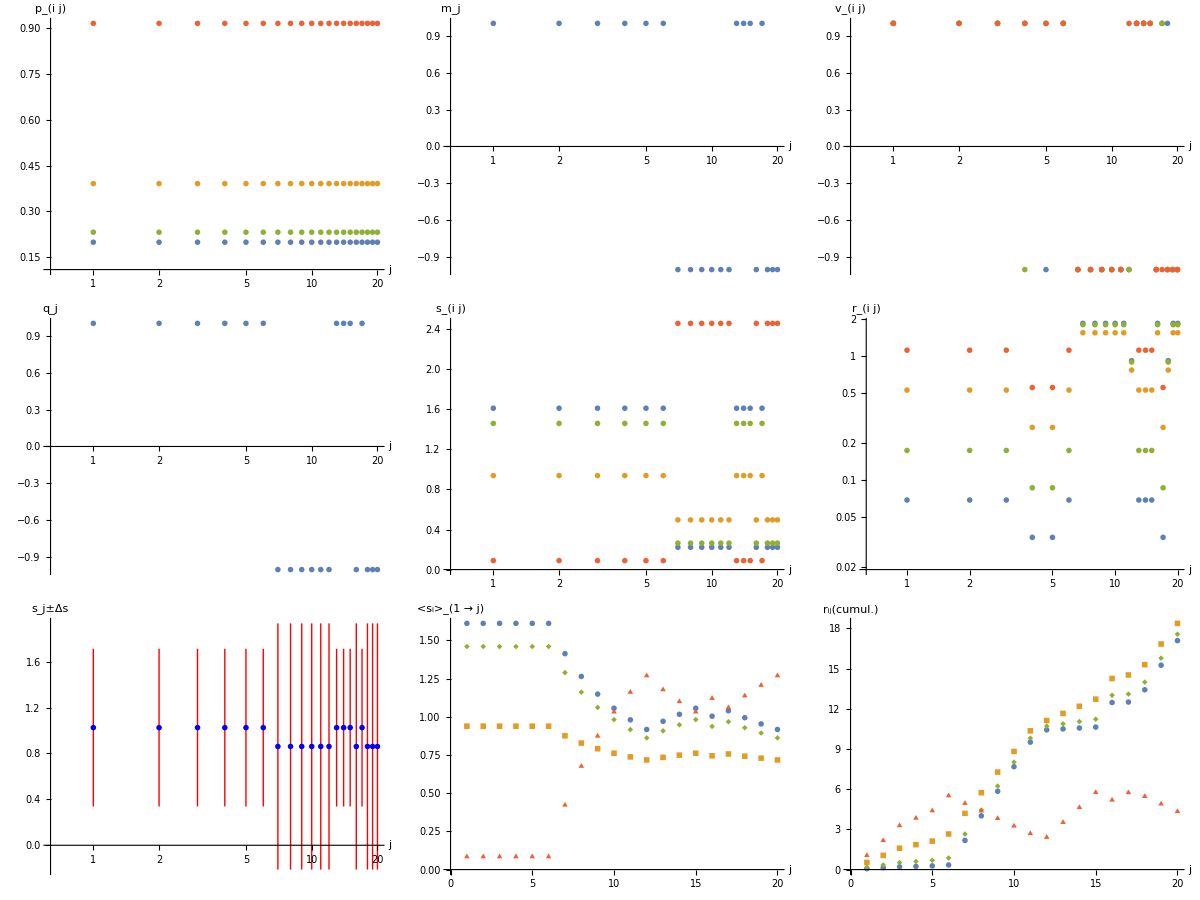

```mathematica
ShowPlots[1]
```

#### Experiments 1 and 2 where done with default functions and default values for ‘nquestions’. To use the custom functions defined above, one needs to load them with ‘SetUserFunctions[]’

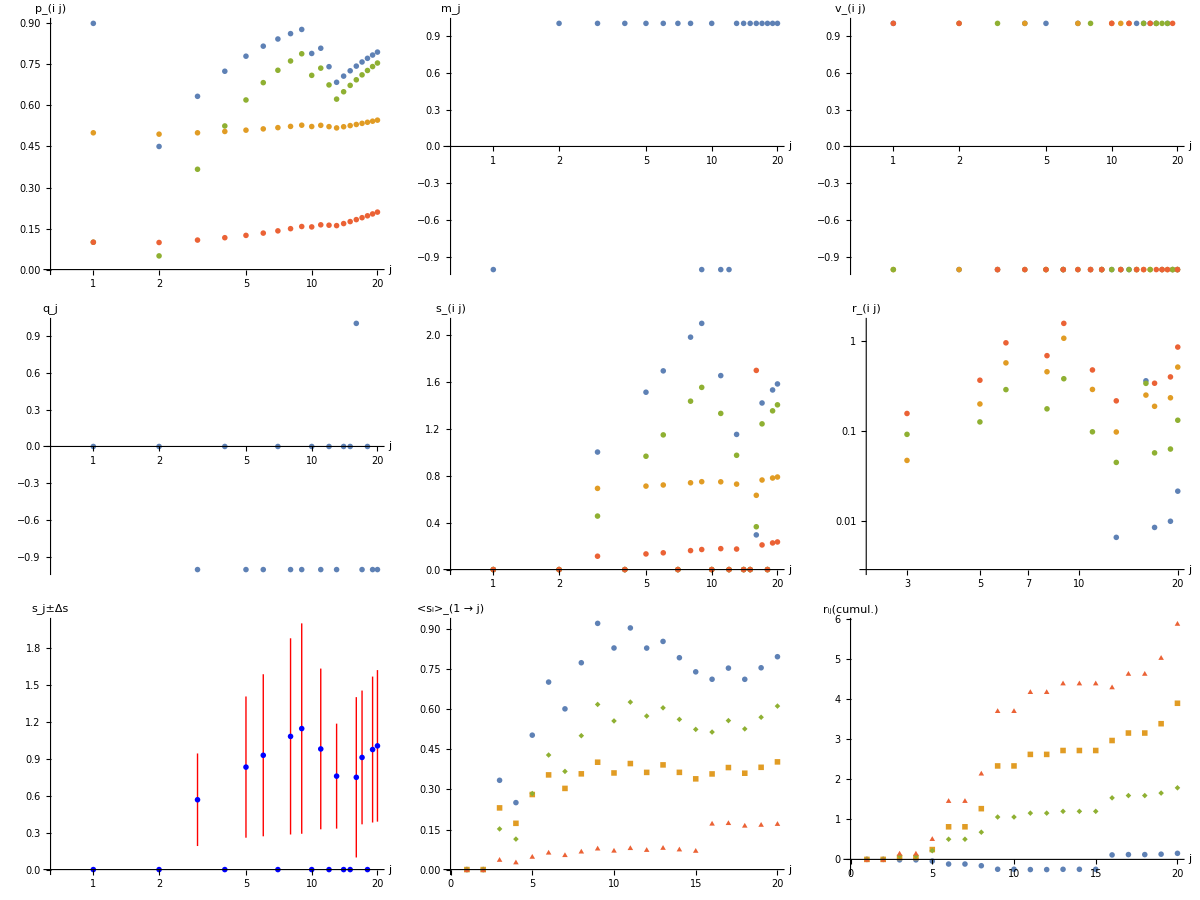

```mathematica
SetUserFunctions[]
RunExperiment[]
ShowPlots[]
```

#### ‘qpredictors’ and ‘nquestions’ can be reinitialized before running another experiment.

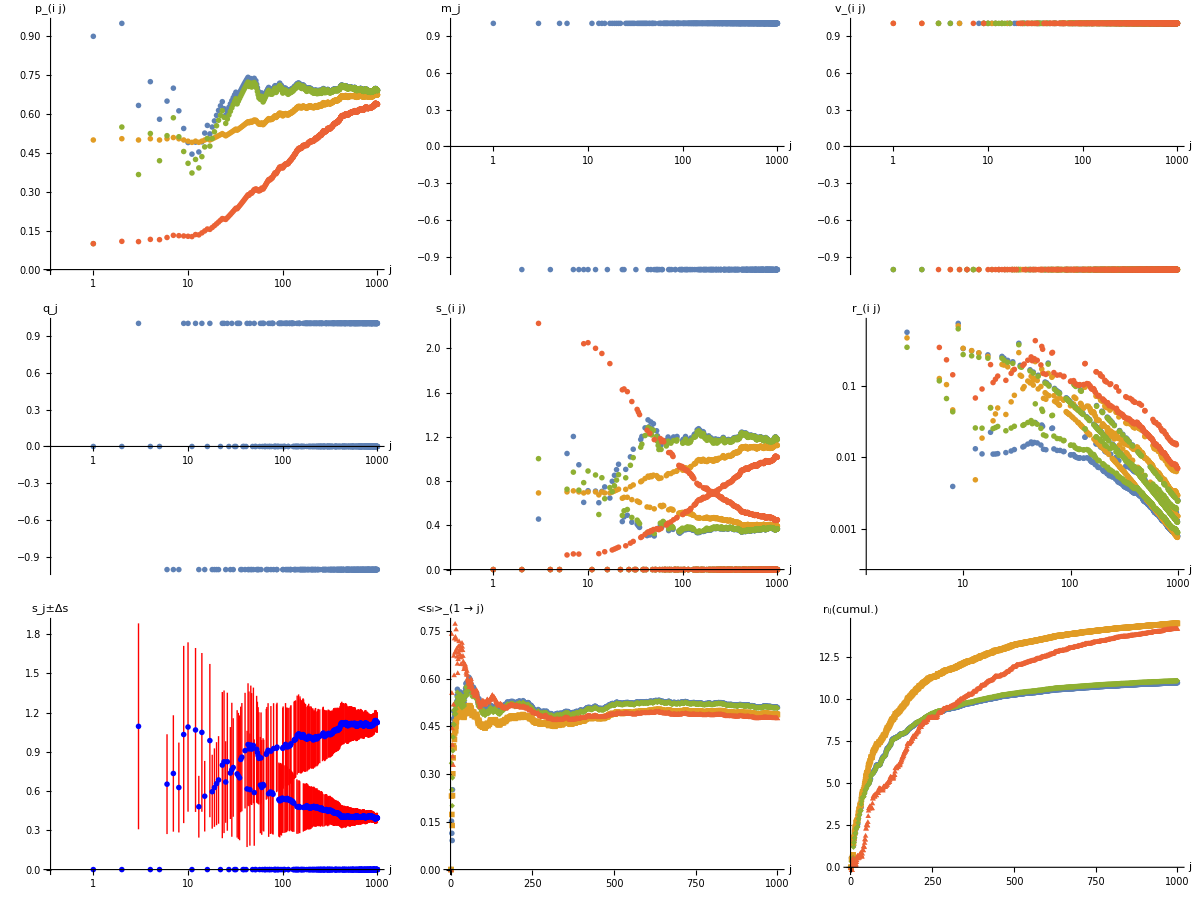

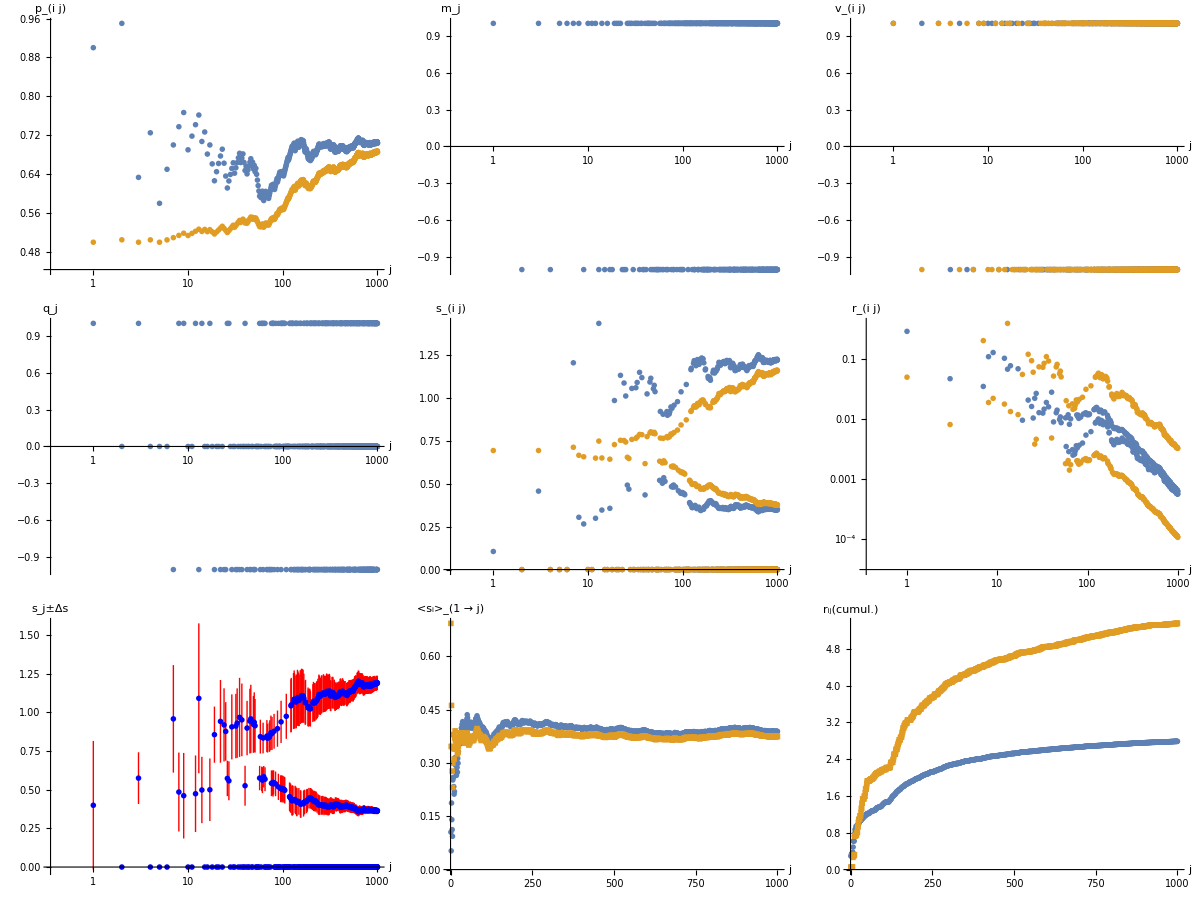

```mathematica
nquestions=1000;
RunExperiment[]
ShowPlots[]

npredictors=2;
RunExperiment[]
ShowPlots[]
```

#### Further display options: the function ‘ShowPlots’ can be called with one or two arguments. ShowPlots[i] ShowPlots[iterator,key] In the first case, ‘i’ is an integer (positive or negative) that correspond to the experiment number: Ex1: ShowPlots[1] --> shows all plots for experiment 1 Ex2: ShowPlots[3] --> shows all plots for experiment 3 Ex3: ShowPlots[-1] --> shows all plots for latest experiment Ex4: ShowPlots[-2] --> shows all plots for second to last experiment In the call with two arguments, iterator can take the same values as those used to access lists in mathematica, while key is a string that represents the type of plot to show (run ShowPlots[1,<anything>] to see available key values.) Ex5: ShowPlots[1,”p”] --> shows the forecasts for experiment 1 Ex6: ShowPlots[-1,“s”] --> shows the surprisal for latest experiments Ex7: ShowPlots[2;;4,”r”] --> shows rewards for experiments 2,3 and 4 Ex8: ShowPlots[All,”rcumul”] --> shows cumulative rewards for all experiments. TODO( FIX THIS ) when showing plots for more than one experiment, plot ranges are set to the smallest possible, so if two experiments are shown with respective x ranges (number of questions) [1,10] and [1,1000] , plot shows only the range [1,10]

```mathematica
RunExperiment[];RunExperiment[];RunExperiment[]
ShowPlots[-2;;-1,"savgj"](* average surprisal for second to last and last experiments*)
```

-Graphics-

```mathematica
ShowPlots[5;;8,"rcumul"](* cumulative surprisal for experiments 5 to 8*)
```

-Graphics-